{1.6095}

{0.725327}

{1.32034/sigma^3}

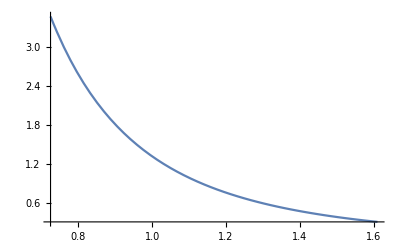

```mathematica
Clear["`*"]
$Assumptions={Element[ratio,Reals],Element[sigmaMax,Reals],Element[sigmaMin,Reals],Element[a,Reals],ratio>1,sigmaMax>0,sigmaMin>0,sigmaMax>sigmaMin};

distribution=a/sigma^3;

ratioValue=ratio->2.219;
ratioRule=sigmaMax->(ratio*sigmaMin);

moment0=Integrate[distribution,{sigma,sigmaMin,sigmaMax}]/.ratioRule;
moment1=Integrate[distribution*sigma,{sigma,sigmaMin,sigmaMax}]/.ratioRule;
subRule=Solve[{moment0==1,moment1==1},{a,sigmaMin}]//FullSimplify;

sigmaMax=sigmaMax/.ratioRule/.subRule/.ratioValue
sigmaMin=sigmaMin/.subRule/.ratioValue

distributionInsert=distribution/.subRule/.ratioRule/.ratioValue//Flatten
Plot[distributionInsert,{sigma,sigmaMin[[1]],sigmaMax[[1]]}]
```